```mathematica
transfers=Solve[transequs,{Pl[s],Vl[s],Bl[s],PHIl[s],Dl[s]}
]//FullSimplify//Flatten;
```

```mathematica
tr=transfers/.paramlist/.{Omega->150,T->70};
```

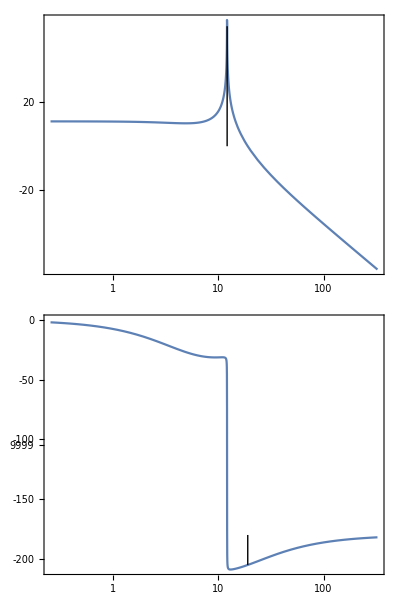

```mathematica
PH=(Pl[s]/.tr)/OLONl[s];
gphi=TransferFunctionModel[PH,s];
BodePlot[gphi,StabilityMargins->True]
```

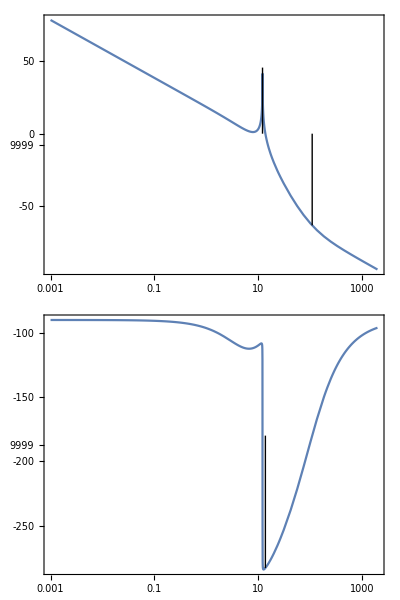

```mathematica
front=TransferFunctionModel[(a(T*s+1))/(T*s+1),s]/.(equs={
12==1/(T √a),
ArcTan[(a-1)/(2 √a)]==π/3
};
Solve[equs,{T,a}]
)[[1]];

lsyss=SystemsModelSeriesConnect[front,gphi];
gc=PIDTune[lsyss,"PID","OpenLoop"];
g=SystemsModelSeriesConnect[gc,TransferFunctionModel[0.01,s]];
BodePlot[g,StabilityMargins->True]
(*Plot[InverseLaplaceTransform[tmp/s,s,t],{t,0,15},PlotRange->All]*)
```

```mathematica
tmp=(g[s]/(1+g[s]))[[1]][[1]]//FullSimplify
```

(6494.09+s (530.52+(8.67761+0.0402184 s) s))/(6494.09+s (1294.27+s (156.839+s (5.2199+1. s))))

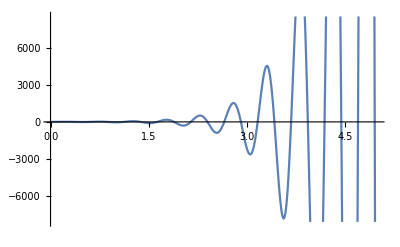

```mathematica
Plot[InverseLaplaceTransform[tmp,s,t],{t,0,5}]
```